# Examples Notebook

## Héctor Manuel Sánchez Castellanos

Sections marked with (*) require the installation of third party applications please read the instruccions file for further instructions

## Import Data and Package

```mathematica
(*Loading package*)
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
(*Load sample songs*)
sampleA=Import[Directory[]<>"/SampleData/CATH1.csv"]//Flatten
sampleB=Import[Directory[]<>"/SampleData/CATH2.csv"]//Flatten
sampleC=Import[Directory[]<>"/SampleData/CATH3.csv"]//Flatten
```

{nay,naw,nay,naw,nay,nea,nec,nbi,nas,nea,nec,nau,nas,nas,nec,nbi,nef,nee,nef,nee,nef,neg,neh,nbd,nbe,nbf,nbn,nbn,nay,naw,nay,naw,nay,naw,naz,nej,naz,nej,naz,nej,naz,nej,naz,nbd,nbj,nbh,nek,nel,nfg,nen,naw,nax,naw,nay,neo,neo,nep,neo,nep,neg,neh,nbd,nbe,neq,neh,nbd,nbe,nbf,nee,nef,nee,nef,nee,nef,ner,nes,nes,nab,nab,nac,nad,net,neu,nbu,nbu,nbh,nbi,nev,nbi,nbi,nbh,nbi,nev,nbi,nbi,nbh,naw,nax,naw,naj,naj,nej,naj,ncv,naj,ncv,nak,nak,nak,neg,neh,nbd,nbe,nbf,ncq,nbg,ncq,ncq,nbg,nbg,ney,nex,nex,ney,nen,nex,nex,ney,nbu,nbu,nbu,nbu,nez,nfa,nfb,nfa,nfb,ner,nes,ner,nab,nab,nac,nad,nab,nac,nad,nad,nfc,nfc,nbu,nax,naw,nay,naw,nbl,naj,nfd,naj,naj,nfd,nak,nak,nak,nff,nbc,nbd,nbe,nbf,ndh,nfg,nem,naw,nax,naw,nay,naw,nay,nfa,nfb,nfb,nfh,nfh,nfh,nfj,nfi,nfh,nfh,nbw,nbw,nbw,nbh,nbi,nev,nbi,nbj,nbh,nbi,nbh,nbj,nbj,nfr,nfl,nfr,nfl,neq,nbc,nbd,nbe,ndx,naj,naj,nfd,nak,nak,nbn,nfn,naw,nax,naw,nay,naw,nfo,nfp,nfp,nfp,nfp,nfq,nfr,nfa,nfb,niy,niy,nbg,nfs,nfc,nbu,nbu,nbu,nbh,nbi,nev,niz,nbj,nbh,nbi,nev,nbi,nat,nau,nav,nas,nas,nat,nau,nav,nas,naj,nfd,naj,nfd,naj,nfd,naj,nfd,nak,nbn,nft,nbv,nfx,nfw,nfg,nen,nfw,nfg,naw,nax,naw,naw,nay,naw,nfj,nfv,nbl,naj,nfd,nag,nbc,nbd,nfy,nag,nbc,nbd,nfy,niy,niy,niy,niy,niy,nas,nas,nat,nau,nav,nas,nfz,nbi,nbj,nfz,nbi,nbj,nbj,nfz,nga,nfz,nbj,nfs,nab,nab,nac,nad,nad,nae,nfc,nae,nbu,nbu,nbu,nbu,naz,nbn,nby,ngb,ncb,ngb,ncb,ngb,nak,nak,nbn,nby,net,naa,naa,naa,naa,nfo,nfr,nfp,nfp,nfp,nfq,nfa,nfb,nfa,nat,nau,nav,nas,nas,nat,nau,nav,nas,nat,nau,nav,nas,nas,nfx,nex,ney,ndh,nex,nex,ney,ngc,naw,nax,naw,nay,naj,nep}

{naa,naa,naa,naa,nab,nab,nac,nad,nab,nac,nad,nae,nae,nae,nae,naf,nag,naf,nag,nag,naf,nag,nah,nai,nah,nai,naj,nfd,naj,nfd,nak,nbn,nfd,nal,naa,naa,nam,nan,nan,nao,nap,nao,nap,nao,nap,naq,nar,nar,nas,nat,nau,nav,nas,nat,nau,nav,nas,nas,naw,nax,naw,nay,naw,nay,naa,naa,nbo,nan,nan,nao,nap,nao,nap,nao,nba,nba,nba,nba,naz,naz,naa,naa,nam,nan,nan,nan,nat,nau,nav,nas,nas,nah,nai,nah,nah,nai,naf,nag,naf,nag,naf,nag,naf,nag,nag,nbc,nbd,nbe,nbe,nbf,niy,niy,nbg,nas,nat,nau,nav,nas,nas,nat,nau,nav,nbh,nbi,nbe,nbi,nbh,nbi,nas,nbh,nai,naa,naa,nbk,nan,nan,nao,nap,nao,nap,naw,nay,naw,niu,naj,naj,nbl,naj,nfh,nfh,nfh,nfh}

{nep,naj,nep,nbn,nbp,nbq,nbq,nbr,nbp,nbq,nam,nbn,nbn,nbn,nao,nap,naq,naw,naq,nar,nbt,nbu,nbu,nbu,nbu,nbv,naa,naa,naa,nbo,nan,nan,nan,nbw,nbw,nbw,naf,nag,naf,nag,nag,naf,nag,nah,nag,nah,nai,nbn,nby,ncb,ncb,nbv,naa,naa,naa,naa,nam,nan,nan,nao,nap,nao,nap,naq,nfh,naq,nat,naq,nar,nar,ndl,ndl,ndl,nbz,ncb,ncc,nhr,nbz,nhr,nbz,ngu,ngv,ncf,ncg,ncg,ncg,ncg,ncg,ncg,naf,nag,nag,naf,nag,naf,nag,naf,nai,nas,nat,nav,nas,nas,nan,nan,ncl,nap,ncl,nap,ncl,nap,nbn,nby,nal,naa,naa,naa,nam,nan,nan,nan,naf,nag,nag,naf,nag,ncg,ncg,ncg,ncg,nbz,nhr,nhj,ncc,nhj,nhr,nbz,nhj,ncc,nhr}

## Auxiliary

```mathematica
(*Get the current installed package version*)
GetPackageVersion[]
```

1.2

```mathematica
(*Filter out phrases that do not conform to nomenclature*)
DeletePhraseIfLonger[{"D","A","E","D","C","BA","rtar","C","B","B","C","A","B","A","A","D","B"},1]
```

{D,A,E,D,C,C,B,B,C,A,B,A,A,D,B}

## TextGrid

```mathematica
ImportSongFromTextGrid[Directory[]<>"/SampleData/CATH1.TextGrid","CATH"];
song=%[[2]]
```

{nay,naw,nay,naw,nay,nea,nec,nbi,nas,nea,nec,nau,nas,nas,nec,nbi,nef,nee,nef,nee,nef,neg,neh,nbd,nbe,nbf,nbn,nbn,nay,naw,nay,naw,nay,naw,naz,nej,naz,nej,naz,nej,naz,nej,naz,nbd,nbj,nbh,nek,nel,nfg,nen,naw,nax,naw,nay,neo,neo,nep,neo,nep,neg,neh,nbd,nbe,neq,neh,nbd,nbe,nbf,nee,nef,nee,nef,nee,nef,ner,nes,nes,nab,nab,nac,nad,net,neu,nbu,nbu,nbh,nbi,nev,nbi,nbi,nbh,nbi,nev,nbi,nbi,nbh,naw,nax,naw,naj,naj,nej,naj,ncv,naj,ncv,nak,nak,nak,neg,neh,nbd,nbe,nbf,ncq,nbg,ncq,ncq,nbg,nbg,ney,nex,nex,ney,nen,nex,nex,ney,nbu,nbu,nbu,nbu,nez,nfa,nfb,nfa,nfb,ner,nes,ner,nab,nab,nac,nad,nab,nac,nad,nad,nfc,nfc,nbu,nax,naw,nay,naw,nbl,naj,nfd,naj,naj,nfd,nak,nak,nak,nff,nbc,nbd,nbe,nbf,ndh,nfg,nem,naw,nax,naw,nay,naw,nay,nfa,nfb,nfb,nfh,nfh,nfh,nfj,nfi,nfh,nfh,nbw,nbw,nbw,nbh,nbi,nev,nbi,nbj,nbh,nbi,nbh,nbj,nbj,nfr,nfl,nfr,nfl,neq,nbc,nbd,nbe,ndx,naj,naj,nfd,nak,nak,nbn,nfn,naw,nax,naw,nay,naw,nfo,nfp,nfp,nfp,nfp,nfq,nfr,nfa,nfb,niy,niy,nbg,nfs,nfc,nbu,nbu,nbu,nbh,nbi,nev,niz,nbj,nbh,nbi,nev,nbi,nat,nau,nav,nas,nas,nat,nau,nav,nas,naj,nfd,naj,nfd,naj,nfd,naj,nfd,nak,nbn,nft,nbv,nfx,nfw,nfg,nen,nfw,nfg,naw,nax,naw,naw,nay,naw,nfj,nfv,nbl,naj,nfd,nag,nbc,nbd,nfy,nag,nbc,nbd,nfy,niy,niy,niy,niy,niy,nas,nas,nat,nau,nav,nas,nfz,nbi,nbj,nfz,nbi,nbj,nbj,nfz,nga,nfz,nbj,nfs,nab,nab,nac,nad,nad,nae,nfc,nae,nbu,nbu,nbu,nbu,naz,nbn,nby,ngb,ncb,ngb,ncb,ngb,nak,nak,nbn,nby,net,naa,naa,naa,naa,nfo,nfr,nfp,nfp,nfp,nfq,nfa,nfb,nfa,nat,nau,nav,nas,nas,nat,nau,nav,nas,nat,nau,nav,nas,nas,nfx,nex,ney,ndh,nex,nex,ney,ngc,naw,nax,naw,nay,naj,nep}

## PhrasesFrequencies

These functions deal with the calculation and display of the frequencies of different phrases in a song

naynawnaynawnayneanecnbinasneanecnaunasnasnecnbinefneenefneenefnegnehnbdnbenbfnbnnbnnaynawnaynawnaynawnaznejnaznejnaznejnaznejnaznbdnbjnbhneknelnfgnennawnaxnawnayneoneonepneonepnegnehnbdnbeneqnehnbdnbenbfneenefneenefneenefnernesnesnabnabnacnadnetneunbunbunbhnbinevnbinbinbhnbinevnbinbinbhnawnaxnawnajnajnejnajncvnajncvnaknaknaknegnehnbdnbenbfncqnbgncqncqnbgnbgneynexnexneynennexnexneynbunbunbunbuneznfanfbnfanfbnernesnernabnabnacnadnabnacnadnadnfcnfcnbunaxnawnaynawnblnajnfdnajnajnfdnaknaknaknffnbcnbdnbenbfndhnfgnemnawnaxnawnaynawnaynfanfbnfbnfhnfhnfhnfjnfinfhnfhnbwnbwnbwnbhnbinevnbinbjnbhnbinbhnbjnbjnfrnflnfrnflneqnbcnbdnbendxnajnajnfdnaknaknbnnfnnawnaxnawnaynawnfonfpnfpnfpnfpnfqnfrnfanfbniyniynbgnfsnfcnbunbunbunbhnbinevniznbjnbhnbinevnbinatnaunavnasnasnatnaunavnasnajnfdnajnfdnajnfdnajnfdnaknbnnftnbvnfxnfwnfgnennfwnfgnawnaxnawnawnaynawnfjnfvnblnajnfdnagnbcnbdnfynagnbcnbdnfyniyniyniyniyniynasnasnatnaunavnasnfznbinbjnfznbinbjnbjnfznganfznbjnfsnabnabnacnadnadnaenfcnaenbunbunbunbunaznbnnbyngbncbngbncbngbnaknaknbnnbynetnaanaanaanaanfonfrnfpnfpnfpnfqnfanfbnfanatnaunavnasnasnatnaunavnasnatnaunavnasnasnfxnexneyndhnexnexneyngcnawnaxnawnaynajnep

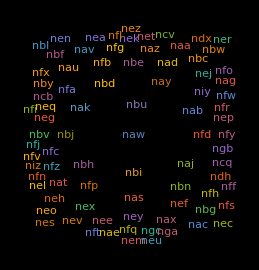

```mathematica
PlotScaledSongWithFrequency[sampleA,2]
WordCloud[song]
```

```mathematica
GetPhrasesFrequencies[sampleA]
GetPhrasesFrequenciesWithPattern[sampleA,(sampleA//GetRepertoire)[[1;;10]]]
```

{{nay,13},{naw,23},{nea,2},{nec,3},{nbi,16},{nas,14},{nau,7},{nef,6},{nee,5},{neg,3},{neh,4},{nbd,9},{nbe,6},{nbf,4},{nbn,6},{naz,6},{nej,5},{nbj,9},{nbh,9},{nek,1},{nel,1},{nfg,4},{nen,3},{nax,7},{neo,3},{nep,3},{neq,2},{ner,3},{nes,3},{nab,7},{nac,4},{nad,6},{net,2},{neu,1},{nbu,14},{nev,5},{naj,15},{ncv,2},{nak,11},{ncq,3},{nbg,4},{ney,5},{nex,7},{nez,1},{nfa,6},{nfb,6},{nfc,4},{nbl,2},{nfd,8},{nff,1},{nbc,4},{ndh,2},{nem,1},{nfh,5},{nfj,2},{nfi,1},{nbw,3},{nfr,4},{nfl,2},{ndx,1},{nfn,1},{nfo,2},{nfp,7},{nfq,2},{niy,7},{nfs,2},{niz,1},{nat,6},{nav,6},{nft,1},{nbv,1},{nfx,2},{nfw,2},{nfv,1},{nag,2},{nfy,2},{nfz,4},{nga,1},{nae,2},{nby,2},{ngb,3},{ncb,2},{naa,4},{ngc,1}}

{{nay,13},{naw,23},{nea,2},{nec,3},{nbi,16},{nas,14},{nau,7},{nef,6},{nee,5},{neg,3}}

```mathematica
GetPhrasesCumulativeFrequencies[sampleA]
GetPhrasesCumulativeFrequenciesWithPattern[sampleA,(sampleA//GetRepertoire)[[1;;10]]]
```

{{nay,13},{naw,36},{nea,38},{nec,41},{nbi,57},{nas,71},{nau,78},{nef,84},{nee,89},{neg,92},{neh,96},{nbd,105},{nbe,111},{nbf,115},{nbn,121},{naz,127},{nej,132},{nbj,141},{nbh,150},{nek,151},{nel,152},{nfg,156},{nen,159},{nax,166},{neo,169},{nep,172},{neq,174},{ner,177},{nes,180},{nab,187},{nac,191},{nad,197},{net,199},{neu,200},{nbu,214},{nev,219},{naj,234},{ncv,236},{nak,247},{ncq,250},{nbg,254},{ney,259},{nex,266},{nez,267},{nfa,273},{nfb,279},{nfc,283},{nbl,285},{nfd,293},{nff,294},{nbc,298},{ndh,300},{nem,301},{nfh,306},{nfj,308},{nfi,309},{nbw,312},{nfr,316},{nfl,318},{ndx,319},{nfn,320},{nfo,322},{nfp,329},{nfq,331},{niy,338},{nfs,340},{niz,341},{nat,347},{nav,353},{nft,354},{nbv,355},{nfx,357},{nfw,359},{nfv,360},{nag,362},{nfy,364},{nfz,368},{nga,369},{nae,371},{nby,373},{ngb,376},{ncb,378},{naa,382},{ngc,383}}

{{nay,13},{naw,36},{nea,38},{nec,41},{nbi,57},{nas,71},{nau,78},{nef,84},{nee,89},{neg,92}}

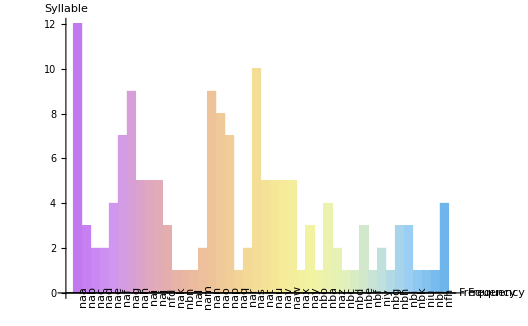

```mathematica
GetPhrasesFrequencies[sampleB];
BarChartPhrasesFrequencies[%]
```

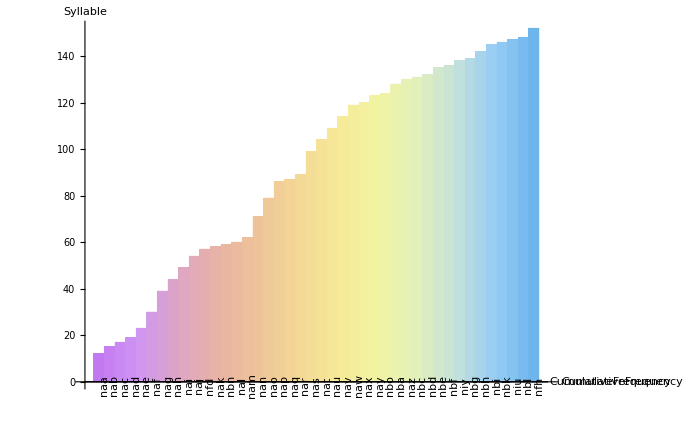

```mathematica
GetPhrasesCumulativeFrequencies[sampleB];
BarChartPhrasesCumulativeFrequencies[%]
```

{{naa,12},{nab,3},{nac,2},{nad,2},{nae,4},{naf,7},{nag,9},{nah,5},{nai,5},{naj,5},{nfd,3},{nak,1},{nbn,1},{nal,1},{nam,2},{nan,9},{nao,8},{nap,7},{naq,1},{nar,2},{nas,10},{nat,5},{nau,5},{nav,5},{naw,5},{nax,1},{nay,3},{nbo,1},{nba,4},{naz,2},{nbc,1},{nbd,1},{nbe,3},{nbf,1},{niy,2},{nbg,1},{nbh,3},{nbi,3},{nbk,1},{niu,1},{nbl,1},{nfh,4}}

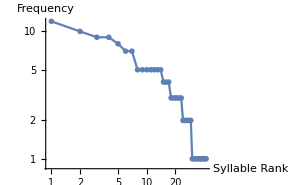

FittedModel[3.32789-0.835876 x]

```mathematica
GetPhrasesFrequencies[sampleB]
LogLogPlotPhrasesFrequencies[%,ImageSize->300]
GetZipfModelFromPhrasesFrequencies[%%,x]
```

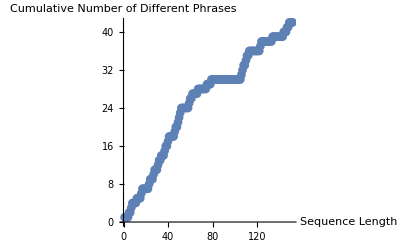

```mathematica
GetCumulativeNumberOfDifferentPhrases[sampleB];
PlotCumulativeNumberOfDifferentPhrases[sampleB]
```

## Repertoire

{nay,naw,nea,nec,nbi,nas,nau,nef,nee,neg,neh,nbd,nbe,nbf,nbn,naz,nej,nbj,nbh,nek,nel,nfg,nen,nax,neo,nep,neq,ner,nes,nab,nac,nad,net,neu,nbu,nev,naj,ncv,nak,ncq,nbg,ney,nex,nez,nfa,nfb,nfc,nbl,nfd,nff,nbc,ndh,nem,nfh,nfj,nfi,nbw,nfr,nfl,ndx,nfn,nfo,nfp,nfq,niy,nfs,niz,nat,nav,nft,nbv,nfx,nfw,nfv,nag,nfy,nfz,nga,nae,nby,ngb,ncb,naa,ngc}

84

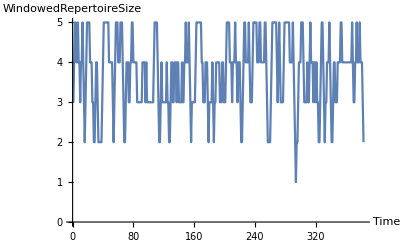

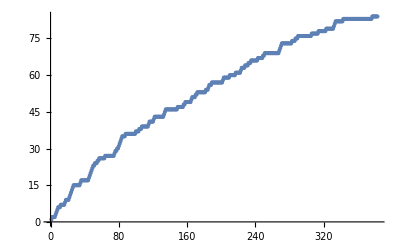

```mathematica
GetRepertoire[sampleA]
GetRepertoireSize[sampleA]
GetWindowedRepertoire[sampleA,5];
GetWindowedRepertoireSize[sampleA,5];
PlotWindowedRepertoireSize[sampleA,5]
GetCumulativeRepertoire[sampleA]//ListPlot
```

```mathematica
GetPairwiseRepertoireSimilarity[sampleA,sampleB]//N
```

0.471405

## Markov

```mathematica
GetTransitionsMarkov[sampleB];
GetTransitionsMarkovWithPattern[sampleB,(sampleB//GetRepertoire)[[1;;10]]]
TableFormTransitions[%%]
```

{{{7/8,1/8,0,0,0,0,0,0,0,0},{0,1/3,2/3,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,1/2,0,0,1/2,0,0,0,0,0},{0,0,0,0,3/4,1/4,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,5/8,1/4,1/8,0,0},{0,0,0,0,0,0,0,1/5,4/5,0},{1/5,0,0,0,0,1/5,0,2/5,0,1/5},{0,0,0,0,0,0,0,0,0,1}},{naa,nab,nac,nad,nae,naf,nag,nah,nai,naj}}

| naa | nab | nac | nad | nae | naf | nag | nah | nai | naj | nfd | nak | nbn | nal | nam | nan | nao | nap | naq | nar | nas | nat | nau | nav | naw | nax | nay | nbo | nba | naz | nbc | nbd | nbe | nbf | niy | nbg | nbh | nbi | nbk | niu | nbl | nfh
naa | 7/12 | 1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/12 | 0 | 0 | 0
nab | 0 | 1/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nac | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nad | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nae | 0 | 0 | 0 | 0 | 3/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naf | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nag | 0 | 0 | 0 | 0 | 0 | 5/9 | 2/9 | 1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nah | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 4/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nai | 1/5 | 0 | 0 | 0 | 0 | 1/5 | 0 | 2/5 | 0 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naj | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 2/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 1/5
nfd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nak | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbn | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nal | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nam | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nan | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/9 | 1/3 | 0 | 0 | 0 | 0 | 1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nao | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nap | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/7 | 0 | 1/7 | 0 | 0 | 0 | 0 | 0 | 1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naq | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nar | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nas | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/10 | 2/5 | 0 | 0 | 1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/10 | 0 | 0 | 0 | 0 | 0
nat | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nau | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nav | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 0 | 0 | 0 | 0 | 0
naw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 3/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | 0 | 0
nax | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nay | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbo | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/4 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naz | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbc | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0
nbf | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
nbg | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0
nbi | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
nbk | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbl | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nfh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
GetTransitionsFrequencies[sampleB];
GetTransitionsFrequenciesWithPattern[sampleB,(sampleB//GetRepertoire)[[1;;10]]]
TableFormTransitions[%%]
```

{{{7,1,0,0,0,0,0,0,0,0},{0,1,2,0,0,0,0,0,0,0},{0,0,0,2,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0},{0,0,0,0,3,1,0,0,0,0},{0,0,0,0,0,0,7,0,0,0},{0,0,0,0,0,5,2,1,0,0},{0,0,0,0,0,0,0,1,4,0},{1,0,0,0,0,1,0,2,0,1},{0,0,0,0,0,0,0,0,0,1}},{naa,nab,nac,nad,nae,naf,nag,nah,nai,naj}}

| naa | nab | nac | nad | nae | naf | nag | nah | nai | naj | nfd | nak | nbn | nal | nam | nan | nao | nap | naq | nar | nas | nat | nau | nav | naw | nax | nay | nbo | nba | naz | nbc | nbd | nbe | nbf | niy | nbg | nbh | nbi | nbk | niu | nbl | nfh
naa | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
nab | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nac | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nad | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nae | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naf | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nag | 0 | 0 | 0 | 0 | 0 | 5 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nah | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nai | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naj | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
nfd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nak | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbn | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nal | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nam | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nan | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nao | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nap | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naq | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nar | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nas | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
nat | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nau | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nav | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
naw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
nax | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nay | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbo | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naz | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbc | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
nbf | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
nbg | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
nbi | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
nbk | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbl | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nfh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3

## Graphs

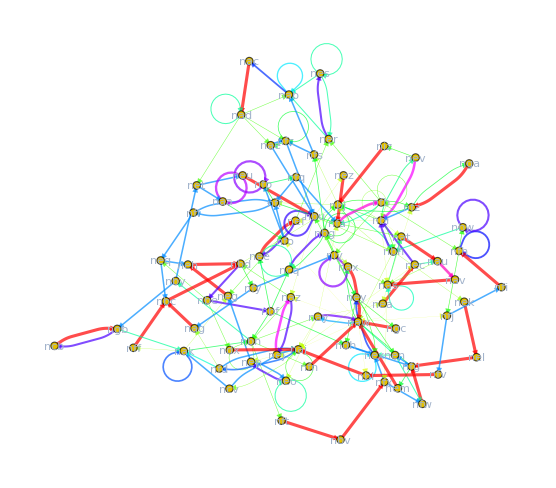

Probability | 0 | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
Color | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

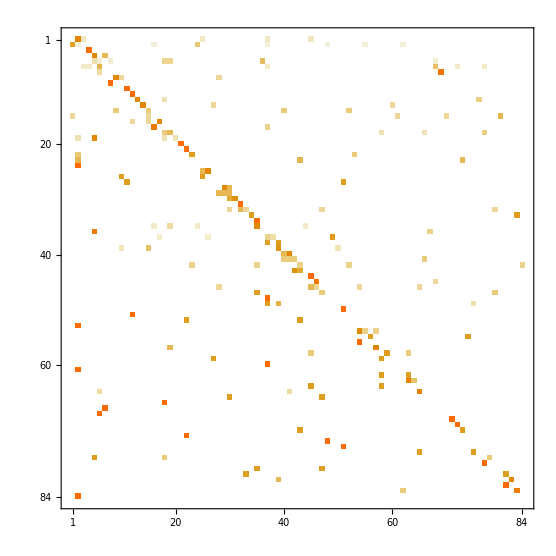

```mathematica
m=GetTransitionsMarkov[sampleA];
GraphTransitionsMarkov[%]
GridColorScaleMarkov[10,10]
m[[1]]//MatrixPlot[#]&
```

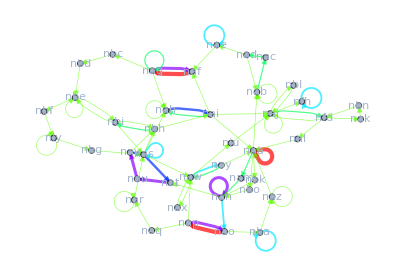

Frequency | 0 | 0.7 | 1.4 | 2.1 | 2.8 | 3.5 | 4.2 | 4.9 | 5.6 | 6.3 | 7.
Color | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
a=GetTransitionsFrequencies[sampleB];
GraphTransitionsFrequencies[a];
b=GetTransitionsGraph[sampleB][[2]]
GridColorScaleFrequency[10,15,a]
```

```mathematica
GetBottlenecks[b,3,3]
GetBranches[b,3,3]
GetOneWays[b,3,3]
GetHourglasses[b,2,2]
```

{{nab,{3,2}},{naf,{3,1}},{nah,{4,2}},{nbn,{3,2}}}

{{nag,{2,4}},{nai,{2,4}},{nak,{2,3}},{nar,{1,3}},{nbo,{2,3}}}

{{nac,{1,1}},{nad,{1,2}},{nae,{2,2}},{nal,{1,1}},{nam,{1,1}},{nan,{1,1}},{nao,{1,1}},{naq,{2,2}},{nas,{1,1}},{nat,{2,2}},{nav,{2,1}},{naw,{1,1}},{nax,{1,2}},{naz,{1,1}},{nba,{1,2}},{nbc,{1,1}},{nbd,{2,2}},{nbe,{2,2}},{nbf,{1,1}},{nbg,{1,1}},{nbi,{1,1}},{nbk,{2,2}},{nbl,{1,1}},{nfd,{1,1}},{nfh,{1,1}},{niu,{1,1}},{niy,{2,1}}}

{{naa,{5,5}},{nab,{3,2}},{nae,{2,2}},{nag,{2,4}},{nah,{4,2}},{nai,{2,4}},{naj,{5,4}},{nak,{2,3}},{nap,{4,3}},{naq,{2,2}},{nat,{2,2}},{nau,{5,5}},{nay,{4,3}},{nbd,{2,2}},{nbe,{2,2}},{nbh,{3,3}},{nbk,{2,2}},{nbn,{3,2}},{nbo,{2,3}}}

```mathematica
ConvertAdjacencyMatrixToEdgesList[a,AllowLoops->True]
```

{{nay,nay,0.},{nay,naw,9.},{nay,nea,1.},{nay,nec,0.},{nay,nbi,0.},{nay,nas,0.},{nay,nau,0.},{nay,nef,0.},{nay,nee,0.},{nay,neg,0.},{nay,neh,0.},{nay,nbd,0.},{nay,nbe,0.},{nay,nbf,0.},{nay,nbn,0.},{nay,naz,0.},{nay,nej,0.},7023,{ngc,nav,0.},{ngc,nft,0.},{ngc,nbv,0.},{ngc,nfx,0.},{ngc,nfw,0.},{ngc,nfv,0.},{ngc,nag,0.},{ngc,nfy,0.},{ngc,nfz,0.},{ngc,nga,0.},{ngc,nae,0.},{ngc,nby,0.},{ngc,ngb,0.},{ngc,ncb,0.},{ngc,naa,0.},{ngc,ngc,0.}}
 |  |  |  |

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

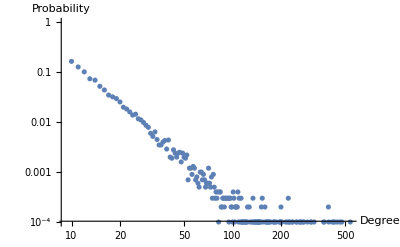
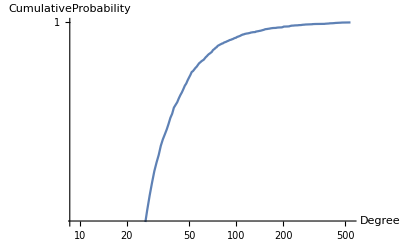
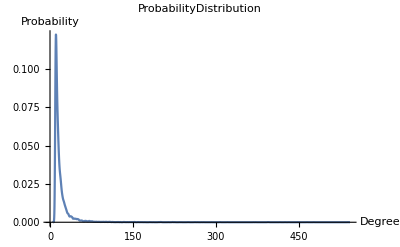

```mathematica
PlotDegreeDistribution[RandomGraph[BarabasiAlbertGraphDistribution[10000,10]]]
```

## SmallWorld

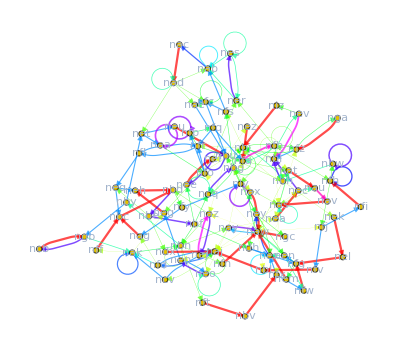

3.90766

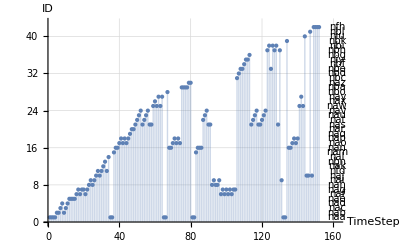

```mathematica
GetTransitionsMarkov[sampleA];
GraphTransitionsMarkov[%]
GetSmallWorldCoefficient[%,1000]//N
ListPlotSong[sampleB,sampleB//GetRepertoire]
```

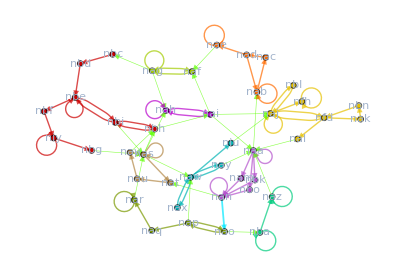

-Graphics-

```mathematica
graph=GetTransitionsGraph[sampleB][[2]];
communities=FindGraphCommunities[graph];
GraphCommunities[graph,communities]
CommunityGraphPlot[graph,communities]
```

```mathematica
GetTransitionsFrequenciesWithPattern[sampleB,sampleB//GetRepertoire];
TableFormCommunities[%,communities]
```

| naa | nab | nac | nad | nae | naf | nag | nah | nai | naj | nfd | nak | nbn | nal | nam | nan | nao | nap | naq | nar | nas | nat | nau | nav | naw | nax | nay | nbo | nba | naz | nbc | nbd | nbe | nbf | niy | nbg | nbh | nbi | nbk | niu | nbl | nfh
naa | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
nab | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nac | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nad | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nae | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naf | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nag | 0 | 0 | 0 | 0 | 0 | 5 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nah | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nai | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naj | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
nfd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nak | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbn | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nal | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nam | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nan | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nao | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nap | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naq | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nar | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nas | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 4 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
nat | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nau | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nav | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
naw | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
nax | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nay | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbo | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nba | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
naz | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbc | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbd | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
nbf | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niy | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
nbg | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
nbi | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
nbk | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
niu | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nbl | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
nfh | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3

```mathematica
freq=GetTransitionsFrequenciesWithPattern[sampleB,sampleB//GetRepertoire];
GetCommunitiesInOutTransitionsFrequencies[{(#/Total[#])&/@freq[[1]]//N,freq[[2]]},communities,CountLoops->True]
GetCommunitiesInOutTransitionsRatios[{(#/Total[#])&/@freq[[1]]//N,freq[[2]]},communities,CountLoops->False]
GetCommunitiesInOutTransitionsGlobalRatio[freq,communities,CountLoops->False]
```

{{6.33333,6.,4.47222,3.75,3.23214,3.5,2.66667,1.77778,1.4,1.5},{1.66667,1.,0.527778,0.25,0.767857,0.5,1.33333,0.222222,0.6,0.5}}

{0.767442,0.827586,0.863309,0.914286,0.780612,0.864865,0.666667,0.875,0.666667,0.333333}

0.788136

```mathematica
freq=GetTransitionsFrequenciesWithPattern[sampleB,sampleB//GetRepertoire];
inOut=GetCommunitiesInOutTransitionsFrequencies[freq,communities,CountLoops->True]
```

{{35.,14.,25.,21.,20.,10.,8.},{3.,1.,3.,3.,5.,1.,2.}}

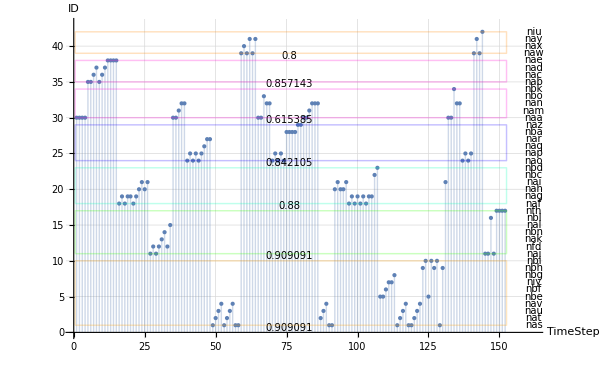

```mathematica
ListPlotSongWithCommunities[sampleB,communities,ImageSize->600,CountLoops->False]
```

## PythonScripts*

```mathematica
SetDirectory[NotebookDirectory[]]
TestScripts[]
```

/Users/chipdelmal/WolframWorkspaces/Base/PajaroLocoPublic/FunctionsUsesExamples

{{SequenceAlignment_LingPy,256},{Collocations_NLTK,0},{Newman,0}}

```mathematica
RunCollocationsScript[sampleB]
```

{0,{{{nag,naf},5},{{nah,nai},4},{{nap,nao},5},{{naf,nag},7},{{nbl,naj},1},{{nad,nab},1},{{nbi,nas},1},{{nai,naf},1},{{naw,niu},1},{{nas,nat},4},{{nag,nbc},1},{{nat,nau},5},{{nbd,nbe},1},{{nbi,nbe},1},{{nav,nas},4},{{nap,naw},1},{{nfd,nal},1},{{nab,nac},2},{{nai,nah},2},{{nbe,nbi},1},{{nag,nah},1},{{naj,nbl},1},{{naw,nay},3},{{nan,nao},3},{{nbf,niy},1},{{nao,nba},1},{{nbi,nbh},1},{{nbh,nbi},2},{{nae,naf},1},{{nas,naw},1},{{naz,naa},1},{{nbc,nbd},1},{{nal,naa},1},{{nay,naa},1},{{nbk,nan},1},{{naa,nam},2},{{nbo,nan},1},{{naw,nax},1},{{nar,nas},1},{{niy,nbg},1},{{nay,naw},2},{{naa,nab},1},{{nak,nbn},1},{{naa,nbo},1},{{naj,nfd},2},{{nbe,nbf},1},{{nbn,nfd},1},{{nau,nav},5},{{nfd,nak},1},{{nac,nad},2},{{nbg,nas},1},{{naa,nbk},1},{{nan,nat},1},{{nam,nan},2},{{nba,naz},1},{{nas,nbh},1},{{nad,nae},1},{{nai,naj},1},{{niu,naj},1},{{nai,naa},1},{{nax,naw},1},{{nbh,nai},1},{{nfd,naj},1},{{naq,nar},1},{{nao,nap},7},{{nav,nbh},1},{{nas,nah},1},{{nap,naq},1},{{naj,nfh},1}},{{{nao,nap},101.472},{{naf,nag},94.4589},{{nat,nau},87.9562},{{nau,nav},87.9562},{{nah,nai},54.0001},{{nap,nao},50.2008},{{nag,naf},46.6963},{{naw,nay},45.5238},{{nac,nad},42.593},{{nas,nat},37.2266},{{nav,nas},37.2266},{{nab,nac},34.9548},{{nbh,nbi},27.3435},{{nak,nbn},24.0823},{{nbc,nbd},24.0823},{{nam,nan},23.5236},{{naj,nfd},21.5757},{{nay,naw},21.5757},{{naa,nam},20.9661},{{naq,nar},18.5372},{{nbf,niy},18.5372},{{niy,nbg},18.5372},{{nbd,nbe},16.4442},{{nbe,nbf},16.4442},{{nbn,nfd},16.4442},{{nfd,nak},16.4442},{{nfd,nal},16.4442},{{nai,nah},15.9175},{{nan,nao},15.7359},{{naj,nbl},14.0743},{{naw,nax},14.0743},{{naw,niu},14.0743},{{nax,naw},14.0743},{{nbl,naj},14.0743},{{niu,naj},14.0743},{{nap,naq},12.5991},{{nag,nbc},11.5244},{{nbk,nan},11.5244},{{nbo,nan},11.5244},{{nbg,nas},11.079},{{nad,nab},10.9525},{{naa,nbk},10.3142},{{naa,nbo},10.3142},{{nal,naa},10.3142},{{nad,nae},9.62034},{{nba,naz},9.62034},{{nbe,nbi},8.91338},{{nbi,nbe},8.91338},{{nbi,nbh},8.91338},{{nav,nbh},6.65235},{{nbh,nai},6.65235},{{nfd,naj},6.65235},{{nar,nas},5.78049},{{naj,nfh},5.40238},{{naz,naa},5.07263},{{nai,naj},4.50167},{{nae,naf},4.09327},{{nas,nbh},3.93586},{{nbi,nas},3.93586},{{nao,nba},3.6038},{{naa,nab},3.28534},{{nay,naa},3.28534},{{nai,naf},3.2487},{{nap,naw},3.2487},{{nag,nah},2.39937},{{nan,nat},2.39937},{{nas,nah},2.06789},{{nas,naw},2.06789},{{nai,naa},1.53332}}}

```mathematica
SetDirectory[NotebookDirectory[]];
GetTransitionsFrequenciesWithPattern[sampleB,sampleB//GetRepertoire];
RunNewmanScript[%]
```

{0,{{naa,nbk,nam,nan,nao,nap,nbo,nba,naz},{naf,nag,nah,nai,nbc,nbd},{nbh,nbi,nas,nat,nau,nav},{nab,nac,nad,nae},{nbl,naj,niu,nfh},{nfd,nak,nbn,nal},{nbe,nbf,niy,nbg},{naw,nax,nay},{naq,nar}},0.615309}

```mathematica
samples={sampleB[[10;;20]],sampleB[[15;;25]],sampleB[[15;;20]]};
validCharacters={"#","$","%","&","*","+","(",")",".",";","<","=",">","?","@","A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z","[","\\","]","^","_","{","|","}","~",".7f",".80",".81",".82",".83",".84",".85",".86",".87",".88",".89",".8a",".8b",".8c",".8d",".8e",".8f",".90",".91",".92",".93",".94",".95",".96",".97",".98",".99",".9a",".9b",".9c",".9d",".9e",".9f"," ","¡","¢","£","¤","¥",".a6","§","¨","©",".aa","«","¬","","®",".af","°","±",".b2",".b3",".b4","µ","¶","·","¸",".b9",".ba","»",".bc",".bd",".be","¿","À","Á","Â","Ã","Ä","Å","Æ","Ç","È","É","Ê","Ë","Ì","Í","Î","Ï","Ð","Ñ","Ò","Ó","Ô","Õ","Ö","×","Ø","Ù","Ú","Û","Ü","Ý","Þ","SS","÷","-"};
RunAlignmentScript[samples,validCharacters][[2]]//GridAlignment
```

nac | nad | nae | nae | nae | nae | naf | nag | naf | nag | nag | - | - | -
- | - | - | nae | naf | nag | naf | nag | nag | naf | nag | nah | nai | nah
- | - | - | - | - | - | - | - | nae | naf | nag | naf | nag | nag

## Co - Occurrences*

```mathematica
CommunityGraphPlot[a,FindGraphCommunities[a]]
```

-Graphics-

/Users/chipdelmal/WolframWorkspaces/Base/PajaroLocoPublic/FunctionsUsesExamples

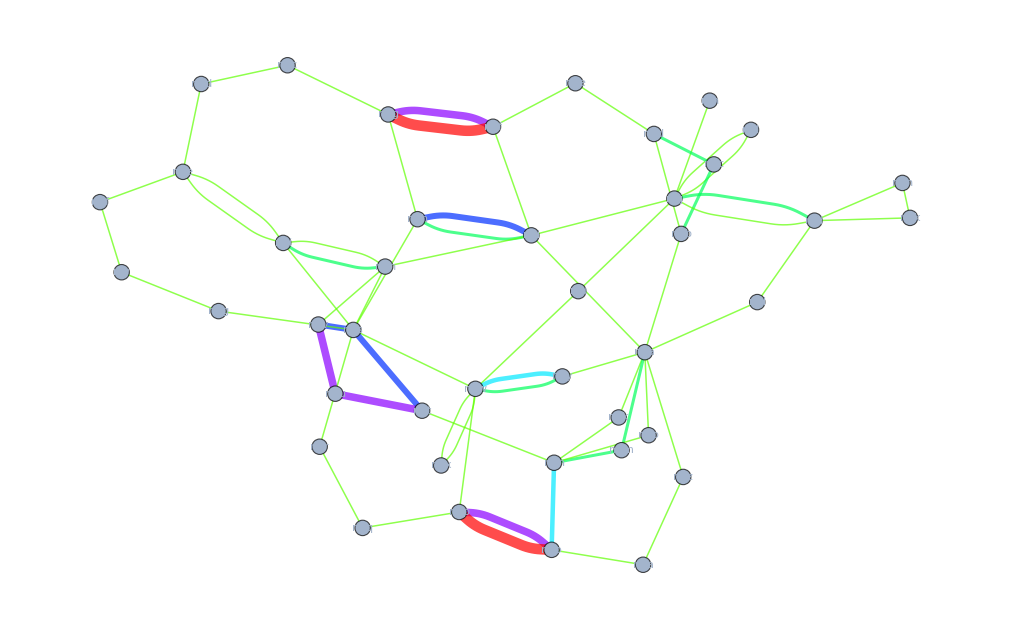

```mathematica
SetDirectory[NotebookDirectory[]]
col=RunCollocationsScript[sampleB];
ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrix[col[[2]]];
a=GraphTransitionsFrequencies[%]
```

## iGraph* (being depreciated)

### RunFunctions

```mathematica
Needs["RLink`"]
SetEnvironment["DYLD_LIBRARY_PATH"->"/Library/Frameworks/R.Framework/Resources/lib"];
InstallR["RHomeLocation"->"/Library/Frameworks/R.Framework/Resources"];
Needs["IGraphR`"]
directory=SetDirectory[NotebookDirectory[]]
rPath="setwd(\"~/"<>(FileNameSplit[directory][[4;;All]]//FileNameJoin)<>"\")";
REvaluate[rPath];
```

InstallR::rundetctd: Failed to detect the R version from the specified path to R home directory. Try using the "RVersion" option to specify the R version explicitly

$Aborted

/Users/chipdelmal/WolframWorkspaces/Base/PajaroLocoPublic/FunctionsUsesExamples

REvaluate::noinst: The R runtime has not been installed. Install it first, by running InstallR

### Export NCOL

```mathematica
frequencyOutput=GetTransitionsFrequenciesWithPattern[randomSample,{"A","B","C","D","E","F","G"}];
ConvertAdjacencyMatrixToiGraphEdgeList[frequencyOutput]
ExportAdjacencyMatrixToNCol[frequencyOutput,"edgelistIn.ncol"]
```

{{0,0,38.},{0,1,40.},{0,2,37.},{0,3,48.},{0,4,32.},{0,5,0.},{0,6,0.},{1,0,37.},{1,1,40.},{1,2,44.},{1,3,43.},{1,4,37.},{1,5,0.},{1,6,0.},{2,0,38.},{2,1,44.},{2,2,48.},{2,3,39.},{2,4,37.},{2,5,0.},{2,6,0.},{3,0,43.},{3,1,39.},{3,2,40.},{3,3,40.},{3,4,48.},{3,5,0.},{3,6,0.},{4,0,39.},{4,1,38.},{4,2,37.},{4,3,40.},{4,4,33.},{4,5,0.},{4,6,0.},{5,0,0.},{5,1,0.},{5,2,0.},{5,3,0.},{5,4,0.},{5,5,0.},{5,6,0.},{6,0,0.},{6,1,0.},{6,2,0.},{6,3,0.},{6,4,0.},{6,5,0.},{6,6,0.}}

### Read NCOL iGraph

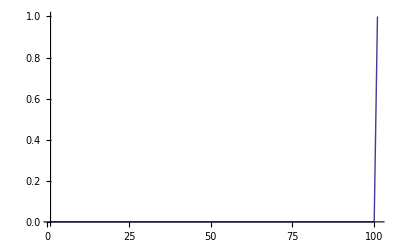

{True}

{False}

```mathematica
REvaluate["G<-read.graph(\"edgelistIn.ncol\", format=\"ncol\",directed=FALSE)"];//Quiet
REvaluate["degree.distribution(G, cumulative = FALSE)"]//ListPlot[#,Joined->True,InterpolationOrder->1,PlotRange->All]&
REvaluate["is.weighted(G)"]
REvaluate["is.directed(G)"]
(*REvaluate["cliques(G)"]*)
```

### Import NCOL

```mathematica
ImportGraphFromNColFile["edgelistOut.ncol",WeightedEdges->False]
ImportGraphFromNColWithPhrasesLabels["edgelistOut.ncol",{"A","B","C","D","E","F","G"}]
```

{{{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}},{0,1,2,3,4,5,6}}

{{{3,3,4,1,0,0,0},{4,2,1,3,1,0,0},{1,2,0,5,1,0,0},{3,1,3,3,3,0,0},{0,2,2,1,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{A,B,C,D,E,F,G}}

### DegreeDistribution

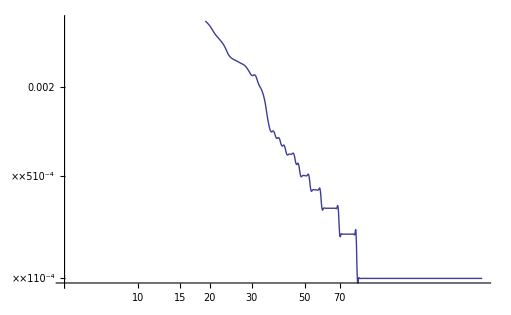

```mathematica
REvaluate["g2 <- barabasi.game(10000)"];
REvaluate["degree.distribution(g2, cumulative = TRUE)"]//ListLogLogPlot[#,Joined->True,InterpolationOrder->2,PlotRange->{0,1}]&
```

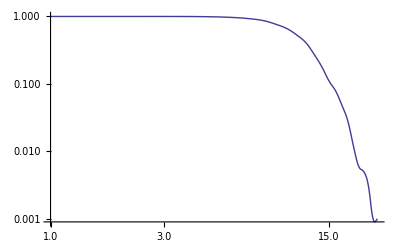

```mathematica
REvaluate["g2 <- erdos.renyi.game(1000,10/1000)"];
REvaluate["degree.distribution(g2, cumulative = TRUE)"]//ListLogLogPlot[#,Joined->True,InterpolationOrder->2]&
```

### FitPowerLaw Custom

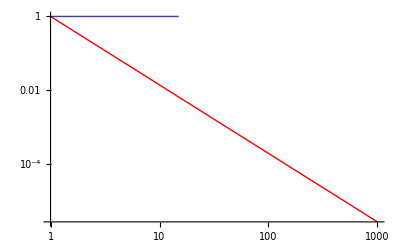
{-Graphics-,{{continuous,False},{alpha,1.85714},{xmin,2.},{logLik,-25.4932},{KS.stat,0.793565},{KS.p,0.000296552}}}

```mathematica
minX=2;
mode="out";
frequencyOutput=GetTransitionsFrequenciesWithPattern[randomSample,{"A","B","C","D","E","F","G"}];
range=1000;


ConvertAdjacencyMatrixToiGraphEdgeList[frequencyOutput];
ExportAdjacencyMatrixToNCol[frequencyOutput,"edgelistIn.ncol"];
REvaluate["G<-read.graph(\"edgelistIn.ncol\", format=\"ncol\",directed=TRUE)"]//Quiet;
REvaluate["d<-degree(G,mode="<>"\""<>mode<>"\""<>")"];
c=REvaluate["fit1<-power.law.fit(d+1,"<>ToString[minX]<>")"];
d={c[[2,1,2]],c[[1]]//Flatten}//Transpose;
b=REvaluate["dd<-degree.distribution(G, cumulative = TRUE)"]//ListLogLogPlot[#,Joined->True,InterpolationOrder->2,PlotRange->{0,1}]&;
a=LogLogPlot[x^(-d[[2,2]]),{x,1,range},PlotStyle->Red];
{Show[a,b],d}
```

### FitPowerLaw Barabasi

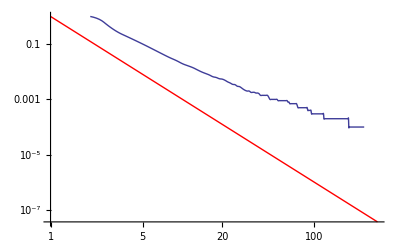
{-Graphics-,{{continuous,False},{alpha,3.},{xmin,10.},{logLik,0.},{KS.stat,0.},{KS.p,1.}}}

```mathematica
REvaluate["g<-barabasi.game(10000)"];
REvaluate["d<-degree(g,mode=\"in\")"];
REvaluate["d<-degree(g,mode="<>"\""<>mode<>"\""<>")"];
c=REvaluate["fit1<-power.law.fit(d+1,10)"];
d={c[[2,1,2]],c[[1]]//Flatten}//Transpose;
b=REvaluate["dd<-degree.distribution(g, cumulative = TRUE)"]//ListLogLogPlot[#,Joined->True,InterpolationOrder->2,PlotRange->{0,1}]&;
a=LogLogPlot[x^(-d[[2,2]]),{x,1,300},PlotStyle->Red];
{Show[a,b],d}
```